```mathematica
D[Exp[-(x1-x2)^2/(2 l^2)],x1,x2]//FullSimplify
```

(ⅇ^(-(x1-x2)^2/(2 l^2)) (l+x1-x2) (l-x1+x2))/l^4

```mathematica
D[Exp[-(x1-x2)^2/(2 l^2)],x1]//FullSimplify
```

(ⅇ^(-(x1-x2)^2/(2 l^2)) (-x1+x2))/l^2

```mathematica
D[(ⅇ^(-(x1-x2)^2/(2 l^2)) (-x1+x2))/l^2,x2]//FullSimplify
```

(ⅇ^(-(x1-x2)^2/(2 l^2)) (l+x1-x2) (l-x1+x2))/l^4

```mathematica
Eigenvalues[{{1,b},{b,1}}]
```

{1-b,1+b}

```mathematica
Inverse[{{1,b},{b,1}}]
```

{{1/(1-b^2),-b/(1-b^2)},{-b/(1-b^2),1/(1-b^2)}}

```mathematica
1/(1-b^2)-b/(1-b^2)//FullSimplify
```

1/(1+b)

```mathematica
-b/(1-b^2)+1/(1-b^2)//FullSimplify
```

1/(1+b)

```mathematica
Eigenvalues[{{1/(1-b^2),-b/(1-b^2)},{-b/(1-b^2),1/(1-b^2)}}]
```

{(-1-b)/(-1+b^2),(-1+b)/(-1+b^2)}

```mathematica
Solve[Exp[-x^2](1-x^2)==-1/10,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[ⅇ^(-x^2) (1-x^2)==-1/10,x]

1

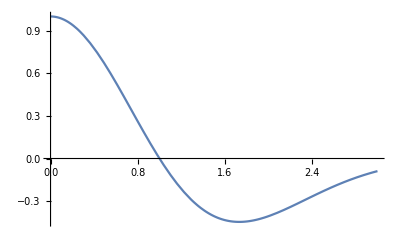

```mathematica
l=1
Plot[Exp[-x^2/(2*l^2)](l^2-x^2)/l^4,{x,0,3}]
```

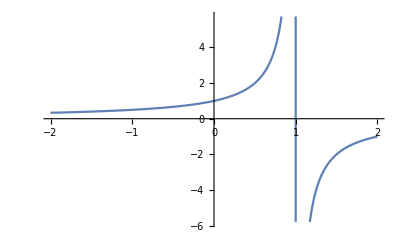

```mathematica
Plot[(-1-b)/(-1+b^2),{b,-2,2}]
```

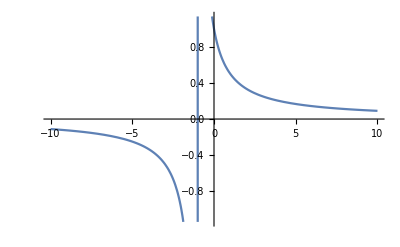

```mathematica
Plot[(-1+b)/(-1+b^2),{b,-10,10}]
```

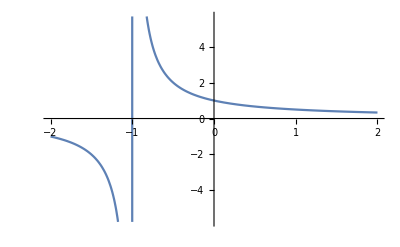

```mathematica
Plot[1/(1+b),{b,-2,2}]
```

```mathematica
b=-0.5
{{1/(1-b^2),-b/(1-b^2)},{-b/(1-b^2),1/(1-b^2)}}
```

-0.5

{{1.33333,0.666667},{0.666667,1.33333}}